# A False Inequality

-Graphics-

## Verification with Monte Carlo

```mathematica
r := RandomInteger[{1,10},3]
```

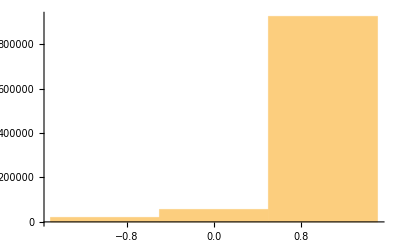

```mathematica
X=Table[a=r;b=r; Sign[Total[a]-Total[b]]Sign[Total[a^(1/p)]-Total[b^(1/p)]],{10^6}]/.p->2 // Histogram
```